```mathematica
Integrate[ Exp[-q( t-s)+c Exp[-b (t-s)]-c],{s,0,t}]
```

∫_0^∞ ⅇ^(-c+c ⅇ^(-b (-s+t))-q (-s+t))ⅆs

```mathematica
Sum[c^k Exp[-c]/k! /(k +n),{k,0,Infinity}]
```

(-c)^-n ⅇ^-c Gamma[n,0,-c]

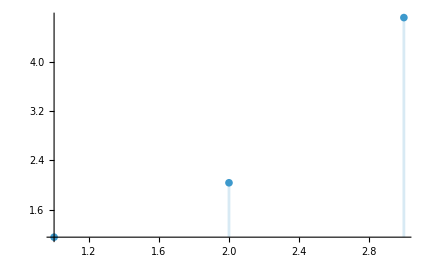

```mathematica
DiscretePlot[(1/Product[N[c(-c)^-n ⅇ^-c Gamma[n,0,-c]],{n,1,M}])/.{c->2},{M,1,3}]
```

```mathematica
Integrate[Exp[c Exp[-x]-c],{x,0,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(c (-1+ⅇ^-x)) does not converge on {0,∞}.

∫_0^∞ ⅇ^(-c+c ⅇ^-x)ⅆx

```mathematica
FullSimplify[D[Exp[c f[b z /(b k +q)]-c],{z,4}]Exp[-c f[b z /(b k +q)]+c]]
```

1/(b k+q)^4 b^4 c (c (c^2 f'[(b z)/(b k+q)]^4+6 c f'[(b z)/(b k+q)]^2 f''[(b z)/(b k+q)]+3 f''[(b z)/(b k+q)]^2+4 f'[(b z)/(b k+q)] f^(3)[(b z)/(b k+q)])+f^(4)[(b z)/(b k+q)])

```mathematica
Sum[c^k Exp[-c]/k! 1/(b k +q)^r,{k,0,Infinity}]
```

∑_(k=0)^∞ (c^k ⅇ^-c (b k+q)^-r)/(k!)

```mathematica
f[r_,c_,b_]:=NIntegrate[x^r Exp[-b x +c Exp[-b x]-c],{x,0,Infinity}]/(r-1)!
g[r_,c_,b_, q_] := NIntegrate[x^r Exp[-q x +c Exp[-b x]-c],{x,0,Infinity}]/(r-1)! / f[r,c,b]
```

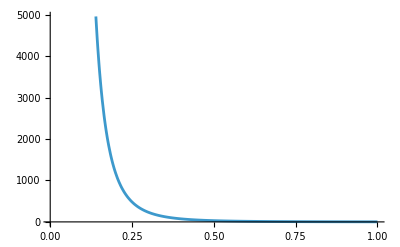

-Graphics-

```mathematica
Plot[f[3,0.5,x],{x,0.001,1}]
Plot[g[3,0.5,x,0.0001],{x,0.001,1}]
```

```mathematica
Integrate[Exp[-I w x +c Exp[-b x]]/(1-Exp[- b x]),x]
```

∫(ⅇ^(c ⅇ^(-b x)-ⅈ w x))/(1-ⅇ^(-b x))ⅆx

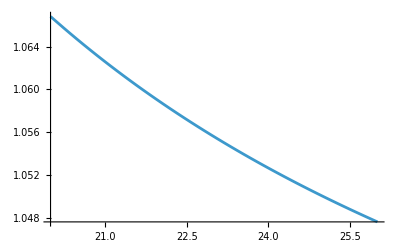

```mathematica
sum1[c_,n_]= Sum[c^k Exp[-c]/k! 1/k,{k,1,n}];
sum2[c_,n_]= Sum[c^k Exp[-c]/k! 1/k^2,{k,1,n}];
sum3[c_,n_]= Sum[c^k Exp[-c]/k! 1/(1+k)^2,{k,0,n}];
moment2[c_,n_]=  sum2[c,n]/sum1[c,n]^2 *1/(1-sum3[c,n]);
Plot[moment2[x,70],{x,20,26}]
```

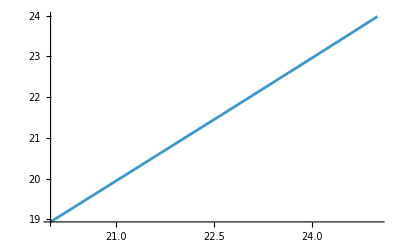

```mathematica
Plot[1/sum1[x,40],{x,20,25}]
```

```mathematica
FullSimplify[DSolve[{f'[x]+ c f[x](1/x-1/x^2)==-b/x^2},f[x],x]]
```

{{f[x]→ⅇ^(-c/x) x^-c (C[1]-b x^(-1+c) ExpIntegralE[c,-c/x])}}

```mathematica
FullSimplify[DSolve[{f''[x]+f'[x](2c+1)/x+  f[x](c^2/x^2-c/x^3)==-b/x^3+c g[x]/x^2},f[x],x]]
```

$Aborted

```mathematica
Plot[ⅇ^(-c/x) x^-c (C[1]-b x^(-1+c) ExpIntegralE[c,-c/x]),{x,0,1}]
```

```mathematica
Product[(1+n/b),{n,1,M}]
```

(1/b)^M Pochhammer[1+b,M]

```mathematica
Sum[(1/b)^M Pochhammer[1+b,M]x^M/M!,{M,0,Infinity}]
```

(b (1-x/b)^-b)/(b-x)

```mathematica
Sum[(1/b)^(2M) (Pochhammer[1+b,M])^2x^M/(M!)^2,{M,0,Infinity}]
```

Hypergeometric2F1[1+b,1+b,1,x/b^2]

```mathematica
Hypergeometric2F2[1+b,1+b,1+c,1+c,1/c]b^2/c
```

(b^2 Hypergeometric2F2[1+b,1+b,1+c,1+c,1/c])/c

```mathematica
Hypergeometric2F2[1+1,1+1,1+25,1+25,1/25]/25
```

1/25 Hypergeometric2F2[2,2,26,26,1/25]

```mathematica
N[HypergeometricPFQ[{2,2},{26,26},1/25]]/25
```

-9.74327×10^46

```mathematica
ExpIntegralEi[("1")/("25")]
```

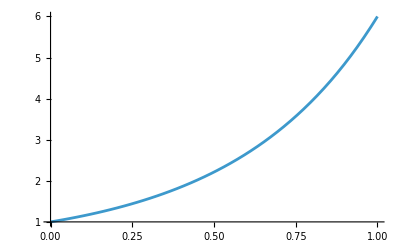

```mathematica
Plot[((1/c)^x Gamma[1+c+x]/Gamma[1+c])/. c->0.2,{x,0,1}]
```

```mathematica
RSolve[ a[n+1]==c a[n]-c,a[n],n]
```

{{a[n]→(c (1-c^n))/(-1+c)+c^(-1+n) C[1]}}

```mathematica
RSolve[a[n]==Sum[c^k Exp[-c]/k! 1/(k+n),{k,0,Infinity}]c a[n+1],a[n],n]
```

{{a[n]→C[1] ∏_(K[1]=1)^(-1+n) ((-c)^K[1] ⅇ^c)/(c (Gamma[K[1]]-Gamma[K[1],-c]))}}

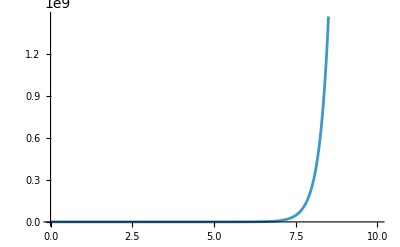

```mathematica
c0 =5;
Plot[(c0^(2-n)+c0^(3-2n))/(c0-1) Pochhammer[1+c0,-1+n]^2,{n,0,10}]
```

NSum::nsnum: Summand (or its derivative) (c^k Exp[-c])/(k! (b k+q+m)^p) is not numerical at point k = 15.

NSum[(c^k Exp[-c])/(k! (b k+q+m)^p),{k,0,∞}]

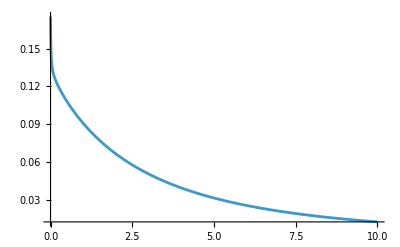

```mathematica
sum1[c_,b_,q_,m_,p_]=NSum[c^k Exp[-c]/k! 1/(b k+q+m)^p,{k,0,Infinity}]
c0=10;
b0=1;
m0=0.01;
Plot[c0 b0  sum1[c0,b0,x,m0,1]/(1-m0 sum1[c0,b0,x,m0,1])-c0 b0/(x+c0 b0),{x,0,10}]
```

```mathematica
P[l_,b_,mu_,q_,p_]=Sum[l^k Exp[-l]/k! /(b k + q +mu)^p,{k,0,Infinity}]
```

∑_(k=0)^∞ (ⅇ^-l l^k (b k+mu+q)^-p)/(k!)

```mathematica
Sum[Product[l^(-j)P[l,b,mu,b j ,2]/P[l,b,mu,b j,1]^2 (1-mu P[l,b,mu,b j ,1])^2,{j,1,n-1}] P[l,b,mu,b n ,2]/P[l,b,mu,b n ,1]^2,{n,1,10}]/.{mu->0,b->1,l->25}
```

NSum::nsnum: Summand (or its derivative) ((∏_(j=1)^(n-1) (l^-j P[l,b,mu,b j,2] (1-mu P[«5»])^2)/P[l,b,mu,Times[«2»],1]^2) P[l,b,mu,b n,2])/P[l,b,mu,b n,1]^2 is not numerical at point n = 1.

1.08714

```mathematica
Sum[Product[l^(-j)P[l,b,mu,b j ,2]/P[l,b,mu,b j,1]^2 (1-mu P[l,b,mu,b j ,1])^2,{j,1,n-1}] P[l,b,mu,b n ,2]/P[l,b,mu,b n ,1]^2,{n,1,10}]/.{mu->0.1,b->1,l->25}
```

General::munfl: (-1.16195×10^-160-8.44209×10^-161 ⅈ) (-3.37812×10^-150-1.03968×10^-149 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.83074×10^-125-8.71212×10^-125 ⅈ) (-5.65917×10^-205-4.11163×10^-205 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-9.76542×10^-172-7.09499×10^-172 ⅈ) (-4.64286×10^-216-3.37323×10^-216 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.08635-5.87306×10^-16 ⅈ

```mathematica
DiscretePlot[Product[((1- mu P[l,b,mu,b j,1])/P[l,b,mu,b j,1])/.{l->0.8,b->0.5,mu->0.00000000001},{j,0,R}],{R,1,100}]
```

-Graphics-

```mathematica
Plot[Sum[Product[l^(-j)P[l,b,mu,b j ,2]/P[l,b,mu,b j,1]^2 (1-mu P[l,b,mu,b j ,1])^2,{j,0,n-1}] P[l,b,mu,b n ,2]/P[l,b,mu,b n ,1]^2,{n,0,3}]/.{mu->0.4,b->0.4},{l,3,10}]
```

$Aborted

```mathematica
Product[l^n b^n P[l,b,mu, n b,1]/(1- mu  P[l,b,mu, n b,1]),{n,1,25}]/.{mu->0.01,b->0.1,l->11}
```

General::munfl: 0.01^300 is too small to represent as a normalized machine number; precision may be lost.

0.+0. ⅈ

General::munfl: 9.01602×10^-131 8.95794×10^-240 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.84493×10^-160 2.70734×10^-294 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.37218×10^-171-2.5865×10^-176 ⅈ) (4.99802×10^-202-9.42104×10^-207 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

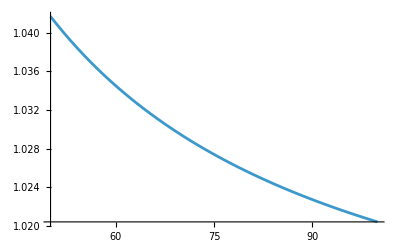

```mathematica
fullanalyticvar = Plot[Sum[Product[l^(-j)P[l,b,mu,b j ,2]/P[l,b,mu,b j,1]^2 (1-mu P[l,b,mu,b j ,1])^2,{j,1,n-1}] P[l,b,mu,b n ,2]/P[l,b,mu,b n ,1]^2,{n,1,10}]/.{mu->0.000001,b->1},{l,50,100}]
```

General::munfl: (1.02586×10^-142-1.9337×10^-147 ⅈ) (1.37218×10^-171-2.5865×10^-176 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.87988×10^-195-2.48309×10^-199 ⅈ) (9.82007×10^-182-1.85104×10^-186 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.87988×10^-195-2.48309×10^-199 ⅈ) (7.79486×10^-249-1.95906×10^-253 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

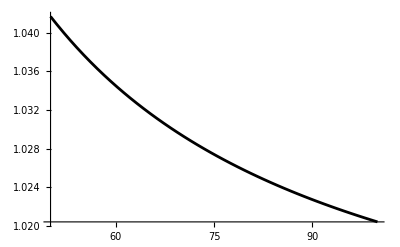

```mathematica
fullNManalyticvar = Plot[Sum[Product[l^(-j)P[l,b,mu,b j ,2]/P[l,b,mu,b j,1]^2 ,{j,1,n-1}] P[l,b,mu,b n ,2]/P[l,b,mu,b n ,1]^2,{n,1,10}]/.{mu->0.000001,b->1},{l,50,100},PlotStyle->Black]
```

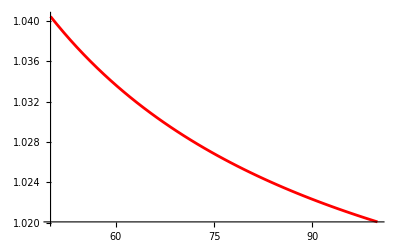

```mathematica
naivevar = Plot[Sum[Product[l^(-j) ,{j,1,n-1}] (1+1/l),{n,1,Infinity}]/.{mu->0.000001,b->1},{l,50,100},PlotStyle->Red]
```

```mathematica
Sum[Product[l^(-j) ,{j,0,n}] (1+1/l),{n,0,Infinity}]
```

1/2 (1+1/l) l^(1/8) EllipticTheta[2,0,1/(√l)]

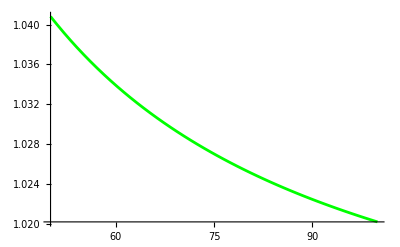

```mathematica
approxvar= Plot[1+2/(l-1),{l,50,100},PlotStyle->Green]
```

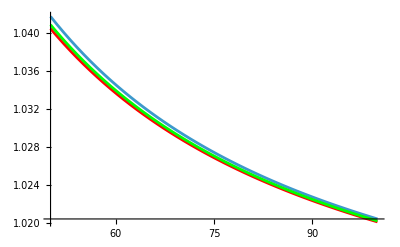

```mathematica
Show[fullanalyticvar,naivevar,approxvar, PlotRange->All]
```

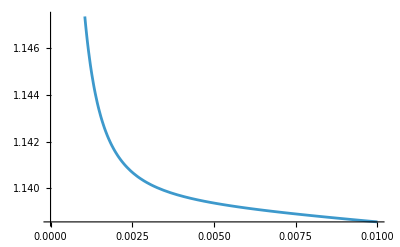

```mathematica
Plot[Sum[Product[l^(-j)P[l,b,mu,b j ,2]/P[l,b,mu,b j,1]^2 (1-mu P[l,b,mu,b j ,1])^2,{j,0,n-1}] P[l,b,mu,b n ,2]/P[l,b,mu,b n ,1]^2,{n,1,10}]/.{b->1,l->25},{mu,0.000000001,0.01}]
```

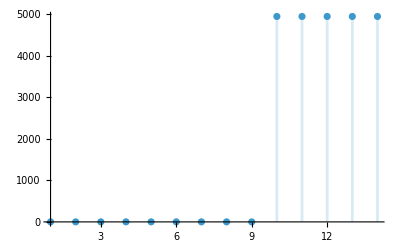

```mathematica
DiscretePlot[(P[l,b,mu,q,p+1]/(P[l,b,mu,q,p]* P[l,b,mu,q,1]))/.{l->100,b->0.5,q->0,mu->0.01},{p,1,14},PlotRange->All]
```

```mathematica
RSolve[{a[n]==1+1/(c) a[n+1],a[R]==0},a[n],n]
```

{{a[n]→-(c^(1-R) (c^n-c^R))/(-1+c)}}

```mathematica
Sum[c^k Exp[-c]/k! 1/(k ),{k,1,Infinity}]
```

-ⅇ^-c (EulerGamma+Gamma[0,-c]+Log[-c])

```mathematica
Series[-((-c)^-mu ⅇ^-c Gamma[1+mu,0,-c])/c(mu+c),{mu,0,0}]
```

(1+O[mu]^1)+Gamma[1+mu,0] (-ⅇ^-c+O[mu]^1)

```mathematica
Integrate[x^(-1)Exp[-x],{x,-3,Infinity}]
```

Integrate::idiv: Integral of ⅇ^-x/x does not converge on {-3,∞}.

∫_-3^∞ ⅇ^-x/x ⅆx

```mathematica
Plot[(P[l,b,mu,q,p+1]/(P[l,b,mu,q,p]*P[l,b,mu,q,p])) /.{b->0.5,q->1,mu->0.01,p->1},{l,10,150}]
```

$Aborted

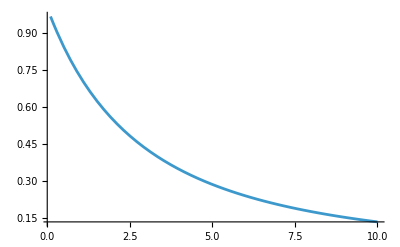

```mathematica
Plot[(1-mu P[l,b,mu,q,1])^2 /.{b->0.5,l->10,q->1},{mu,0.1,10}]
```

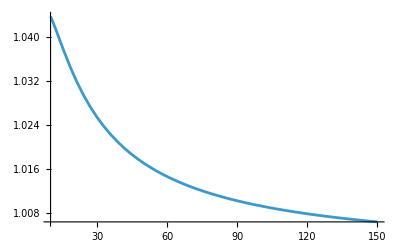

```mathematica
Plot[(P[l,b,mu,q,2]/(P[l,b,mu,q,1] P[l,b,mu,q,1])) /.{b->0.1,q->0.1,mu->0.5},{l,10,150}]
```

```mathematica
RSolve[{a[n] == 1/l (1-mu P[l,b,mu,b n,1])^2a[n+1] + P[],a[R]==0},a[n],n]
```

$Aborted

```mathematica
Binomial[7,2]
```

21

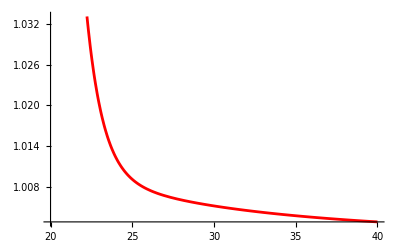

```mathematica
betaver =Plot[1+(P[l,b,mu,q,2]/(1- mu P[l,b,mu,q,1])^2 (1/(1- l b^2 P[l,b,mu,b,2])))/.{b->0.5,q->0,mu->0.0001},{l,20,40},PlotStyle->Red]
```

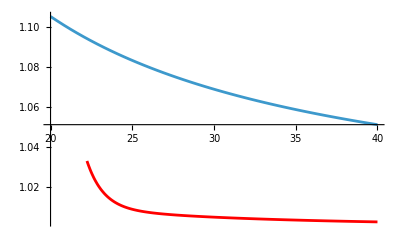

```mathematica
Show[approxvar, betaver,PlotRange->All]
```

```mathematica
RSolve[a[n] == 1 +1/c +(1-0.5  P[c,0.1,0.5,0,1])^2 a[n]/c,a[n],n]
```

```mathematica
{{a[n]->(1. ⅇ^(2. c)+1. c ⅇ^(2. c))/(-1. ⅇ^(2. c)+1. c ⅇ^(2. c)+2. ⅇ^c Hypergeometric1F1[5.,6.,1. c]-1. Hypergeometric1F1[5.,6.,1. c]^2)}}
```

```mathematica
((1. ⅇ^(2. c)+1. c ⅇ^(2. c))/(-1. ⅇ^(2. c)+1. c ⅇ^(2. c)+2. ⅇ^c Hypergeometric1F1[5.,6.,1. c]-1. Hypergeometric1F1[5.,6.,1. c]^2))/.{c->20}
```

1.08411

```mathematica
dq = ( c/(1+(1- mu P[c,0.1,0.5,0,1] )^2 1.08411))/.{c->20,mu->0.5}
```

11.8899

```mathematica
Sum[c^j 1/(mu+j b),{j,0,r}]
```

(LerchPhi[c,1,mu/b]-c^(1+r) LerchPhi[c,1,1+mu/b+r])/b

```mathematica
Sum[c^r Exp[-I mu Psi (LerchPhi[c,1,mu/b]-c^(1+r) LerchPhi[c,1,1+mu/b+r])/b],{r,0,Infinity}]
```

∑_(r=0)^∞ c^r ⅇ^(-(ⅈ mu Psi (LerchPhi[c,1,mu/b]-c^(1+r) LerchPhi[c,1,1+mu/b+r]))/b)

```mathematica
FullSimplify[(i b + mu - mu (mu+ i b)/(mu+b+b i ) -i b (mu+ i b)/(mu+b+b i )^2 )/.{mu->0}]
```

(i (-i+b (1+i)^2))/(1+i)^2

```mathematica
Product[(i b +c i b - i^2 c b /(1+i)^2),{i,1,j-1}]
```

((b (1+c))^(-1+j) Pochhammer[(4+3 c-√(-c (4+3 c)))/(2+2 c),-1+j] Pochhammer[(4+3 c+√(-c (4+3 c)))/(2+2 c),-1+j])/(j Gamma[1+j])

```mathematica
Product[(i b +c i b - i^2 c b /(1+i)^2),{i,1,j-1}]
```

```mathematica
Sum[x^j c^j /j ((b (1+c))^(-1+j) Pochhammer[(4+3 c-√(-c (4+3 c)))/(2+2 c),-1+j] Pochhammer[(4+3 c+√(-c (4+3 c)))/(2+2 c),-1+j])/(j Gamma[1+j]),{j,0,r}]
```

Power::infy: Infinite expression 1/0^2 encountered.

∑_(j=0)^r (c^j (b (1+c))^(-1+j) Pochhammer[(4+3 c-√(-c (4+3 c)))/(2+2 c),-1+j] Pochhammer[(4+3 c+√(-c (4+3 c)))/(2+2 c),-1+j])/(j^2 Gamma[1+j])

```mathematica
Plot[Sum[x^j c^j /j (b^(-1+j) c mu Gamma[1/2+c/2-(√((b+b c)^2))/(2 b)+j] Gamma[1/2 (1+c+(√(b^2 (1+c)^2))/b+2 j)])/(Gamma[1/2 (3+c-(√(b^2 (1+c)^2))/b)] Gamma[(√(b^2 (1+c)^2)+b (3+c))/(2 b)] Gamma[1+j]),{j,1,r}]/.{mu->0.01,c->0.9,b->0.5,r->3},{x,1,3}]
```

-Graphics-

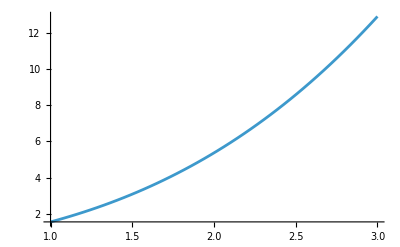

```mathematica
Plot[Sum[x^j c^j /j ,{j,1,r}]/.{c->0.9,b->0.5,r->3},{x,1,3}]
```

```mathematica
Product[i b + c (i b^2 + mu b)/(mu + b (1+i)),{i,0,j-1}]
```

(b^j c mu Pochhammer[(3 b+b c+mu-√(-4 b c mu+(b+b c+mu)^2))/(2 b),-1+j] Pochhammer[(3 b+b c+mu+√(-4 b c mu+(b+b c+mu)^2))/(2 b),-1+j])/((b+mu) Pochhammer[2+mu/b,-1+j])

```mathematica
Product[i b + c (i b^2 )/(b (1+i)),{i,0,j-1}]
```

0

```mathematica
Series[(b^j c mu Pochhammer[(3 b+b c+mu-√(-4 b c mu+(b+b c+mu)^2))/(2 b),-1+j] Pochhammer[(3 b+b c+mu+√(-4 b c mu+(b+b c+mu)^2))/(2 b),-1+j])/((b+mu) Pochhammer[2+mu/b,-1+j]),{mu,0,1}]
```

(b^(-1+j) c Gamma[1/2+c/2-(√((b+b c)^2))/(2 b)+j] Gamma[1/2 (1+c+(√(b^2 (1+c)^2))/b+2 j)] mu)/(Gamma[1/2 (3+c-(√(b^2 (1+c)^2))/b)] Gamma[(√(b^2 (1+c)^2)+b (3+c))/(2 b)] Gamma[1+j])+O[mu]^2

(b^(-1+j) c mu Gamma[1/2+c/2-(√((b+b c)^2))/(2 b)+j] Gamma[1/2 (1+c+(√(b^2 (1+c)^2))/b+2 j)])/(Gamma[1/2 (3+c-(√(b^2 (1+c)^2))/b)] Gamma[(√(b^2 (1+c)^2)+b (3+c))/(2 b)] Gamma[1+j])

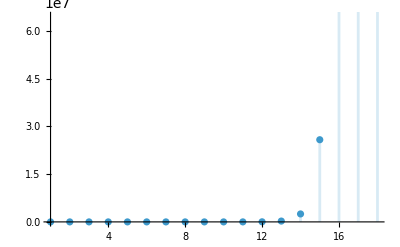

```mathematica
DiscretePlot[(b^(-1+j) c Gamma[1/2+c/2-(√((b+b c)^2))/(2 b)+j] Gamma[1/2 (1+c+(√(b^2 (1+c)^2))/b+2 j)] mu)/(Gamma[1/2 (3+c-(√(b^2 (1+c)^2))/b)] Gamma[(√(b^2 (1+c)^2)+b (3+c))/(2 b)] Gamma[1+j])/.{b->0.7,mu->0.01,c->0.8},{j,1,18}]
```

```mathematica
DiscretePlot[(b^(-1+j) c Gamma[1+c+ j] mu)/(Gamma[2+c]j)/.{b->0.7,mu->0.01,c->0.8},{j,1,18}]
```

-Graphics-

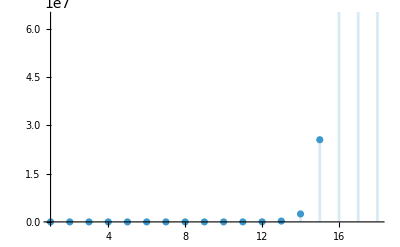

```mathematica
DiscretePlot[(b^j c mu Pochhammer[(3 b+b c+mu-√(-4 b c mu+(b+b c+mu)^2))/(2 b),-1+j] Pochhammer[(3 b+b c+mu+√(-4 b c mu+(b+b c+mu)^2))/(2 b),-1+j])/((b+mu) Pochhammer[2+mu/b,-1+j])/.{b->0.7,mu->0.01,c->0.8},{j,1,18}]
```

```mathematica
Sum[(b^(-1+j) c^(-j+1) Gamma[1+c+ j] mu)/(Gamma[2+c]j^2 b),{j,1,r}]
```

(c mu [1+r])/(b^2 Gamma[2+c])

```mathematica
Plot[(1-c b P[c,b,mu,b,1]- mu P[c,b,mu,0,1])/.{b->0.5,mu->0.1},{c,1.1,10}]
```

-Graphics-

```mathematica
(1-c b P[c,b,mu,b,1]- mu P[c,b,mu,0,1])/.{b->0.5,mu->0.1,c->20}
```

2.66454×10^-15+1.85241×10^-16 ⅈ

```mathematica
Sum[c^k Exp[-c]/k! 1/(k)^4,{k,1,Infinity}]
```

c ⅇ^-c HypergeometricPFQ[{1,1,1,1,1},{2,2,2,2,2},c]

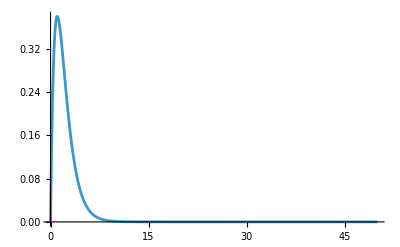

```mathematica
Plot[c ⅇ^-c HypergeometricPFQ[{1,1,1,1,1},{2,2,2,2,2},c],{c,0,50},PlotRange->All]
```

```mathematica
Integrate[Exp[I b s]BesselJ[0,2 c Sqrt[t a/(a b + z^2)]],{b,-Infinity,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(ⅈ b s) BesselJ[0,2 c √((a t)/(Times[«2»]+Power[«2»]))] does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(ⅈ b s) BesselJ[0,2 c √((a t)/(a b+z^2))]ⅆb